# Enzyme Kinetics

## A computational study towards understanding enzyme catalyzed reactions

Emma Hokken 10572090
Natasja Wezel 11027649

### 1. Michaelis-Menten Kinetics Introduction: About Michaelis-Menten

We consider a simple enzyme catalyzed reaction where an enzyme E catalyzes the reaction of substrate S to form a product P. Here, ES is the enzyme-substrate complex in which the enzyme and substrate are bound together. This reaction looks as follows:

     E + S (⇌_(k_-1))^(k_(+1)) ES →^(k_(+2)) E + P
     
Here, we assume that the reaction is in a steady state. If E_0 denotes the total concentration of the enzyme, the overall reaction rate can be described by the Michaelis-Menten equation. The equation looks as follows:

V = V_max S /( S+ K_M) 

Here, V_maxdenotes the maximum velocity (k_(+2) E_0) and K_M = (k_-1 + k_(+2))/(k_(+1)) denotes the Michaelis-Menten constant. This constant represents the substrate concentration where the reaction rate is half of V_max. 

Some enzymes do not cause a reaction that increases the rate of a reaction, but cause a reduction in this rate. These enzymes are often called inhibitors. In this section, three inhibitors are considered:

V_c = (V_max S)/(S+ (1+ I/K_i)K_M) 

V_n = (V_max S)/((1 + I/K_i)( S + K_M))

V_u = (V_max S)/((1 + I/K_i)S + K_M)

-Graphics-Figure 1: An example of noncompetitive inhibition

Because we are talking about reversible inhibition, the binding of the inhibitor has a dissociation constant: K_i. The subscripts c, n, and u stand for competitive, non-competitive, and uncompetitive. Competitive inhibitors work by binding at the active site on the enzyme. They compete with the substrate for the active site and prevent it from binding. Noncompetitive inhibitors have a separate binding site on the enzyme and can bind to the enzyme or the enzyme-substrate complex. Uncompetitive inhibitors have a separate binding site on the enzyme but only bind to the enzyme when the substrate is bound to the enzyme.

Methods
In order to investigate the behaviour of Michaelis-Mentis kinetics, a few experiments are performed. Firstly, a plot is generated where the values of V_max, K_M and the maximum substrate concentration can be varied using sliders. In order to generate this plot, the Michaelis-Menten function was initialized with certain values, after which a manipulate-able plot was generated. 

After that, we take a look at the behaviour of the equation when considering different kinds of inhibitors (V_c, V_n, V_u). This is done for two different settings. First, considering a constant concentration I (= 5) but varying K_i. Second, considering a constant concentration K_i (= 2) but varying I. In order to run this, the three different functions were initialized. For the plotting of the functions, K_i varied from 0.001 to 0.401, taking steps of 0.1. For the plotting of a varying I, I varied from 50 to 250, taking steps of 50.

Results and Discussion
We first looked into general behavior of enzymes by making a plot in which you can vary the different factors that influence the Michaelis-Menten kinetics of the reaction as described in the introduction. This behaviour of the Michaelis-Menten equation is displayed in the figure below.

```mathematica
ClearAll["Global`*"]

V[S_,Km_,Vmax_]=Vmax (S/(Km+S));

Manipulate[
Plot[
Evaluate[{V[S,Km,Vmax],Vmax}],
{S,0.,Smax},
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
ImageSize->Large,
PlotLabel->"Michaelis-Menten kinetics",
PlotStyle->{Dashing[{0.05,0.}],Dashing[{0.05,0.05}]},
PlotRange->All,
PlotLegends->{"V", "Vmax"},
AxesOrigin->{0,0}], 
{{Km, 10}, 0, 100, Appearance->"Labeled"}, 
{{Vmax, 10}, 0, 100, Appearance->"Labeled"}, 
{{Smax, 100}, 50, 1000, Appearance->"Labeled"} ]
```

Varying V_max only results in a change in the range of the y-axis; the form of the curve itself does not change. Increasing the substrate concentration results in a faster approach to V_max. Increasing K_m has to opposite effect: this results in a slower approach to V_max. 

Next, we look at the behaviour of the Michaelis-Menten equation when considering three different kinds of inhibitors: competitive, non-competitive, and uncompetitive. The plot below displays the three different inhibitors with varying K_i.

```mathematica
Vcompetitive[S_,Vmax_,Iconc_,Ki_,Km_] =( Vmax * S )/ (S + (1+ Iconc/Ki)*Km);
Vnoncompetitive[S_,Vmax_,Iconc_,Ki_,Km_] = (Vmax*S)/((1+Iconc/Ki)*(S +Km));
Vuncompetitive[S_,Vmax_,Iconc_,Ki_,Km_]=(Vmax*S)/((1+Iconc/Ki)S + Km);
```

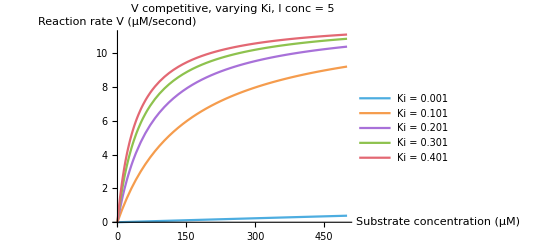

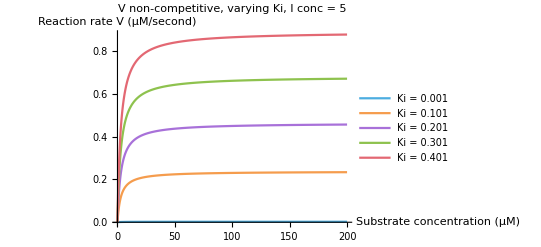

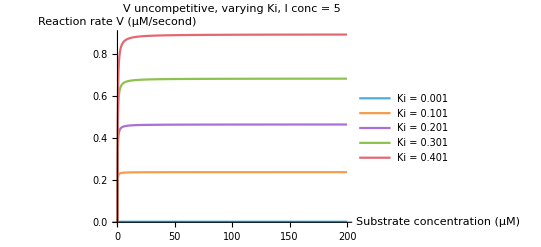

```mathematica
VcompKi = Plot[Evaluate@Table[Vcompetitive[S, 12, 5, Kii, 3], {Kii,0.001,0.5,0.1}], {S,0.,500}, 
PlotLabel->"V competitive, varying Ki, I conc = 5",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
PlotTheme->"PastelColor",
PlotLegends->{"Ki = 0.001","Ki = 0.101", "Ki = 0.201","Ki = 0.301", "Ki = 0.401"}]

VncompKi = Plot[Evaluate@Table[Vnoncompetitive[S, 12, 5, Kii, 3], {Kii,0.001,0.5,0.1}], {S,0.,200},
PlotLabel->"V non-competitive, varying Ki, I conc = 5",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
PlotTheme->"PastelColor",
PlotLegends->{"Ki = 0.001", "Ki = 0.101", "Ki = 0.201","Ki = 0.301", "Ki = 0.401"}]

VucompKi = Plot[Evaluate@Table[Vuncompetitive[S, 12, 5, Kii, 3], {Kii,0.001,0.5,0.1}], {S,0.,200}, 
PlotLabel->"V uncompetitive, varying Ki, I conc = 5",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
PlotTheme->"PastelColor",
PlotLegends->{"Ki = 0.001", "Ki = 0.101", "Ki = 0.201","Ki = 0.301", "Ki = 0.401"}]
```

Here we see that, for the competitive inhibitor, when the K_i increases, the reaction rate also increases faster. We also see that the V_max is not influenced in this case: the all the lines seem to still be going to the V_max, albeit really slow for K_i= 0.001. The same goes for the non-competitive and uncompetitive inhibitors. These reach their “plateaus” earlier than the competitive one. The graphs of the non-competitive and uncompetitive inhibitors have the same shape, but the uncompetitive inhibitor goes up faster than the non-competitive inhibitor.

Next, we plotted the same kinds of graphs, but with varying inhibitor concentration.

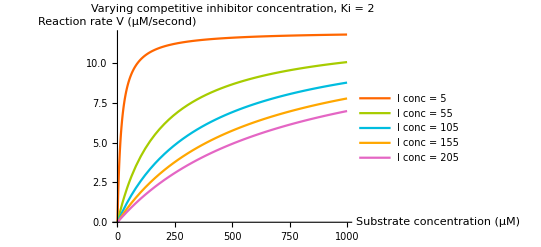

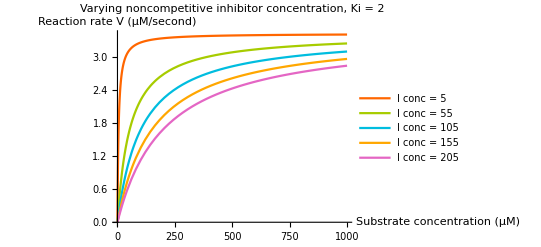

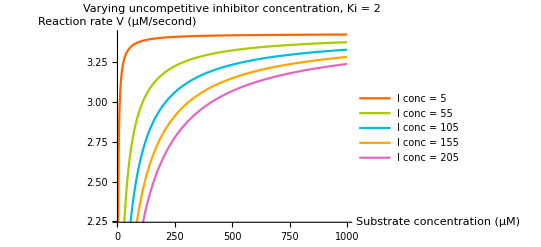

```mathematica
VcompI = Plot[Evaluate@Table[Vcompetitive[S, 12, 5, 2, ConcII], {ConcII,5,250,50}], {S,0.,1000}, 
PlotLabel->"Varying competitive inhibitor concentration, Ki = 2",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
PlotTheme->"NeonColor",
PlotLegends->{"I conc = 5", "I conc = 55", "I conc = 105","I conc = 155", "I conc = 205"}]

VncompI = Plot[Evaluate@Table[Vnoncompetitive[S, 12, 5, 2, ConcII], {ConcII,5,250,50}], {S,0.,1000}, 
PlotLabel->"Varying noncompetitive inhibitor concentration, Ki = 2",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"}, 
PlotTheme->"NeonColor",
PlotLegends->{"I conc = 5", "I conc = 55", "I conc = 105","I conc = 155", "I conc = 205"}]

VucompI = Plot[Evaluate@Table[Vuncompetitive[S, 12, 5, 2, ConcII], {ConcII,5,250,50}], {S,0.,1000}, 
PlotLabel->"Varying uncompetitive inhibitor concentration, Ki = 2",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"}, 
PlotTheme->"NeonColor",
PlotLegends->{"I conc = 5", "I conc = 55", "I conc = 105","I conc = 155", "I conc = 205"}]
```

When we vary the concentration of the inhibitor, we see that the line of the reaction rate changes. For the competitive inhibitor, we see that the substrate concentration keeps increasing, and again, we don not really see it reaching the plateau of maximum speed for the higher inhibitor concentrations. For the non-competitive and uncompetitive inhibitors, we do see that they reach their plateau, and that this V_max gets lower when the inhibitor concentration increases. The big difference between non-competitive and uncompetitive seems to be the reaction rate. For the non-competitive inhibitor, there is a larger difference in the reaction rate between an I concentration of 5 and 55 than there is for this rate in the uncompetitive inhibitor. Also, the reaction rate for an I concentration 205 in the non-competitive inhibitor is much lower that the rate of the uncompetitive inhibitor for the same I concentration.

Conclusions
Competitive inhibitors cause an increase in K_m, but do not affect the overall efficacy of the enzyme. Noncompetitive inhibitors reduce the number of active enzyme molecules and thus lower the V_max. Uncompetitive inhibitor reduce the amount of ES available and thus less S to create the half of ES. This leaves us with a lower K_m. There is a reduced amount of ES that is not abound to the ESI, so at high substrate concentrations we have a lower V_(max.)

2. Enzymes and inhibitors

Introduction: About Enzymes and inhibitors
A Lineweaver-Burke plot is a plot where the inverse of the reaction velocity is plotted against the inverse of the substrate concentration (1/Vagainst 1/S). This kind of plot can easily be used to calculate the Michaelis-Menten parameters. Furthermore, the plot can be used to distinguish between different types of inhibitors. 

In this section, we take a closer look at enzymes and inhibitors

Methods
In order to take a closer look at enzymes and inhibitors, the below data is given. The data is a generated list {{S, V},...,...} of measured concentrations and reaction rates. We plot the data and the Michaelis-Menten parameters are retrieved. V_maxis read from the plot directly, and K_M is derived from V_max (as K_M = 1/2 V_max).

```mathematica
measuredData = {{0, 0}, {0.86,6.666},{2.16,8.},{3.18,8.571},{4.02,8.889},{5.12,9.091},{6.19,9.231},{7.15,9.333},{7.98,9.412},{8.94,9.474},{10.,9.524},{11.03,9.565},{11.94,9.6},{12.96,9.63},{13.87,9.655},{15.07,9.678},{16.14,9.697},{17.17,9.714},{17.88,9.729},{19.17,9.743},{19.81,9.756},{21.04,9.767}};
```

After this, we generate the Lineweaver-Burke plots and retrieve the Michaelis-Menten parameters from those. The Lineweaver-Burk (double-reciprocal) plot of 1/v against 1/s gives intercepts at 1/Vmax and -1/Km. From this, the parameters can be inferred. We compare the calculated parameters from the Lineweaver-Burke plot with the estimated parameters from the Michaelis-Menten plot.

Lastly, the below data was given. This is data from measurements with multiple concentrations of an inhibitor (I = 2, 5, 8). We try to find out what kind of inhibitor it is by using the Lineweaver-Burk plot. We also investigate whether the Michaelis-Menten parameters change. The latter is achieved by finding the best fit for the different inhibitor concentrations and determining the Michaelis-Menten parameters based on this fit.

```mathematica
dataI2={{0,0},{0.97,2.381},{1.88,3.571},{2.8,4.286},{3.85,4.762},{4.91,5.102},{5.85,5.357},{6.82,5.556},{7.8,5.714},{8.86,5.844},{10.02,5.952},{10.95,6.044},{12.19,6.123},{13.01,6.19},{14.01,6.25},{15.15,6.303},{16.16,6.349},{16.92,6.391},{18.12,6.429},{18.82,6.463},{19.97,6.494},{21.03,6.522},{22.01,6.548},{22.91,6.571},{23.91,6.593},{24.96,6.614},{26.13,6.633},{27.2,6.65},{28.06,6.667},{28.98,6.682},{30.04,6.697},{30.97,6.71},{32.17,6.723},{33.14,6.735},{34.12,6.746},{34.82,6.757},{35.89,6.767},{37.04,6.777},{38.14,6.786},{38.84,6.794},{39.88,6.803},{40.99,6.811},{42.09,6.818},{42.99,6.826},{44.14,6.832},{45.13,6.839},{45.84,6.845},{46.81,6.851},{48.07,6.857},{49.1,6.863},{49.88,6.868},{51.15,6.873},{52.18,6.878},{52.89,6.883},{53.92,6.888},{55.11,6.892},{56.08,6.897},{57.06,6.901},{58.14,6.905},{59.13,6.909},{59.89,6.912},{60.92,6.916},{62.08,6.92},{62.83,6.923},{64.15,6.927},{65.,6.93},{66.05,6.933},{66.86,6.936},{67.91,6.939},{69.01,6.942},{70.12,6.944},{70.96,6.947},{71.83,6.95},{73.08,6.952},{73.97,6.955},{75.01,6.957},{75.96,6.96},{77.08,6.962},{78.,6.964},{79.09,6.967},{80.05,6.968},{80.86,6.971},{82.18,6.973},{82.84,6.975},{83.99,6.977},{84.85,6.979},{85.92,6.98},{86.88,6.983},{87.95,6.984},{88.96,6.986},{90.11,6.988},{91.07,6.989},{92.09,6.991},{93.15,6.993},{94.19,6.994},{94.91,6.996},{96.02,6.997},{97.13,6.998},{98.02,7.},{99.09,7.001},{99.95,7.003}};

dataI5 = {{0,0},{1.03,1.667},{1.81,2.5},{2.83,3.},{4.08,3.333},{5.06,3.572},{5.87,3.75},{6.89,3.889},{8.16,4.},{8.97,4.091},{9.92,4.167},{10.82,4.231},{11.95,4.286},{13.01,4.333},{14.16,4.375},{15.1,4.412},{15.88,4.444},{17.01,4.474},{17.94,4.5},{19.2,4.524},{20.08,4.546},{20.99,4.565},{22.11,4.583},{22.93,4.6},{24.04,4.615},{24.84,4.629},{25.98,4.643},{26.81,4.655},{28.02,4.667},{28.82,4.677},{30.1,4.687},{30.87,4.697},{32.1,4.706},{33.19,4.714},{34.08,4.722},{34.97,4.73},{36.16,4.737},{37.16,4.744},{37.86,4.75},{38.85,4.756},{39.89,4.762},{40.94,4.767},{42.08,4.773},{43.01,4.778},{43.81,4.783},{44.82,4.787},{46.13,4.792},{47.02,4.796},{47.92,4.8},{49.13,4.804},{50.15,4.808},{51.04,4.811},{51.91,4.815},{52.85,4.818},{54.17,4.821},{55.02,4.825},{55.95,4.828},{56.83,4.83},{58.01,4.833},{59.02,4.836},{59.94,4.839},{61.19,4.841},{62.16,4.844},{63.09,4.846},{64.15,4.848},{65.01,4.851},{65.82,4.853},{66.86,4.855},{67.99,4.857},{68.91,4.859},{69.98,4.861},{71.12,4.863},{72.13,4.865},{72.94,4.867},{74.08,4.869},{74.92,4.87},{75.94,4.872},{76.93,4.874},{77.99,4.875},{79.06,4.876},{80.02,4.878},{81.13,4.88},{81.97,4.881},{82.88,4.882},{83.89,4.884},{84.84,4.885},{85.97,4.886},{86.94,4.888},{88.,4.889},{89.09,4.89},{89.92,4.891},{90.99,4.893},{91.82,4.894},{92.91,4.895},{94.07,4.896},{94.94,4.897},{95.92,4.898},{97.,4.899},{97.82,4.9},{99.13,4.901},{99.93,4.902}};

dataI8 = {{0,0},{1.,1.282},{1.86,1.923},{3.05,2.308},{4.,2.564},{4.99,2.747},{6.01,2.885},{7.19,2.992},{8.14,3.077},{9.06,3.147},{10.,3.205},{11.15,3.255},{11.82,3.297},{12.98,3.333},{14.17,3.365},{15.16,3.394},{15.86,3.419},{17.03,3.441},{18.08,3.462},{18.99,3.48},{19.83,3.497},{21.1,3.512},{22.18,3.526},{23.19,3.538},{23.83,3.55},{25.17,3.561},{25.96,3.572},{27.05,3.581},{28.02,3.59},{28.92,3.598},{29.86,3.606},{30.98,3.613},{32.07,3.62},{32.95,3.626},{33.84,3.633},{34.89,3.638},{35.85,3.644},{37.17,3.649},{38.17,3.654},{39.06,3.658},{39.93,3.663},{41.11,3.667},{42.06,3.671},{42.91,3.675},{43.99,3.679},{44.92,3.683},{45.84,3.686},{46.91,3.689},{47.85,3.692},{49.05,3.696},{49.98,3.698},{50.9,3.701},{51.84,3.704},{52.85,3.706},{54.09,3.709},{55.,3.711},{55.87,3.713},{56.82,3.716},{57.91,3.718},{59.04,3.72},{60.09,3.722},{61.18,3.724},{62.18,3.726},{62.95,3.728},{63.96,3.73},{64.93,3.731},{66.11,3.733},{67.,3.735},{68.18,3.736},{68.9,3.738},{70.06,3.739},{70.86,3.741},{72.03,3.742},{73.16,3.744},{73.91,3.745},{75.06,3.746},{76.15,3.747},{77.08,3.749},{77.83,3.75},{79.04,3.751},{79.98,3.752},{81.15,3.753},{82.,3.755},{82.98,3.756},{84.03,3.757},{84.92,3.758},{85.97,3.759},{87.,3.76},{88.17,3.761},{89.2,3.762},{90.02,3.763},{90.87,3.763},{92.18,3.764},{92.81,3.765},{94.2,3.766},{95.12,3.767},{95.83,3.768},{97.04,3.768},{97.91,3.769},{99.1,3.77},{99.87,3.771}};
```

Results and Discussion
The below plot represents the measured data with corresponding V_max and K_M.

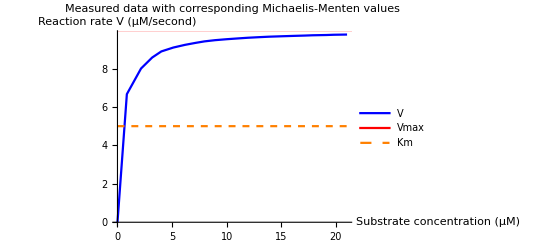

```mathematica
line = ListLinePlot[measuredData, PlotLegends->{"V"}, PlotStyle->Blue];
vmax = Plot[10 ,{x, 0, 25},PlotStyle->Red, PlotLegends->{"Vmax"}];
km = Plot[5, {x, 0 ,25},PlotStyle->{Dashed, Orange}, PlotLegends->{"Km"}];
Show[line, vmax,km , 
PlotLabel-> "Measured data with corresponding Michaelis-Menten values", 
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
ImageSize-> "Large"]
```

In this plot, a horizontal line is plotted to show how you can read off the K_m, at the intersection of the graph and this line. The Michaelis-Menten parameters are as follows: V_max ≈ 10 and K_M≈ 1.

Next, the Lineweaver-Burke plot is generated and can be seen below.

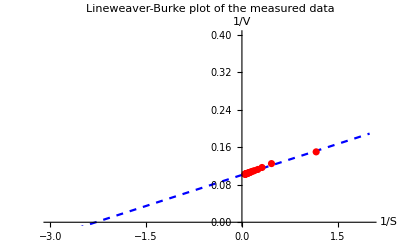

```mathematica
lineweaverburkData = 1/measuredData⟦2 ;;⟧;
lm = LinearModelFit[lineweaverburkData, x, x];

Show[Plot[lm[x], {x, -3, 2}, PlotStyle->{Dashed, Blue}], ListPlot[lineweaverburkData, PlotStyle->Red], 
PlotRange->{{-3 , 2}, {0,0.4}},
PlotLabel-> "Lineweaver-Burke plot of the measured data",
AxesLabel-> {"1/S", "1/V"}]
```

```mathematica
Vmax = 1/lm[0]
Km = -((k/.Solve[lm[k] == 0, Reals])^-1)⟦1⟧
```

9.91677

0.436726

V_max is retrieved from the intersection of the line with the y-axes (so x = 0) and K_M is retrieved from the intersection of the line with the x-axes (so where y = 0).  We see that our estimation of V_(max_□)is quite close to the one calculated here. But the K_m estimation is pretty poor, since the calculated one is only half of that.

Next, we investigate the data retrieved from measurements with different concentrations of a certain inhibitor. First, the data is plotted and the Michaelis-Menten parameters are retrieved.

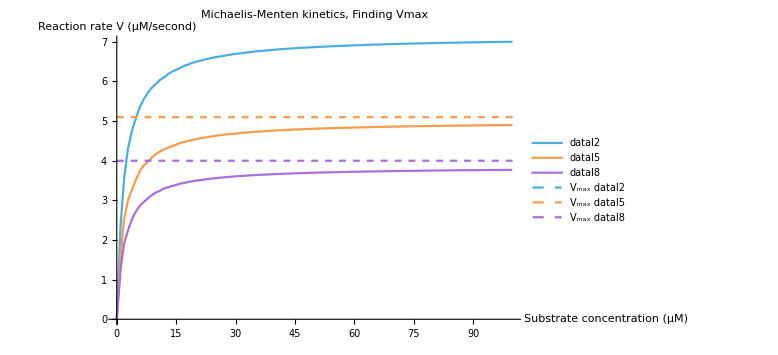

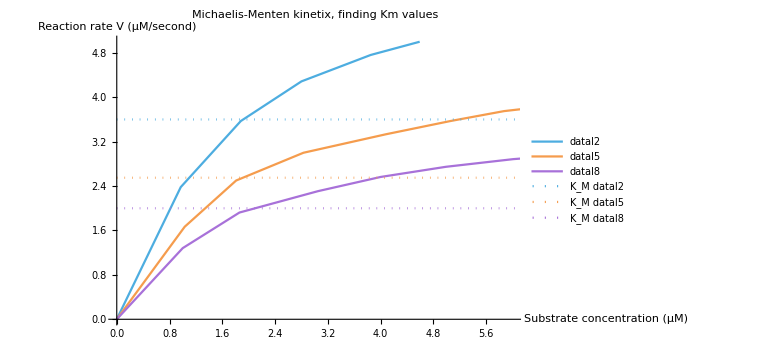

I concentration | I = 2 | I = 5 | I = 8
V_max | 7.2 | 5.1 | 4.
K_M | 2. | 2. | 2.

```mathematica
dataPlot = ListLinePlot[{dataI2, dataI5, dataI8}, 
PlotLegends->{"dataI2", "dataI5", "dataI8"},
PlotTheme->"PastelColor"];
Vmaxes = Plot[{7.2, 5.1, 4.0}, {x, 0, 100}, PlotStyle->Dashed, 
PlotLegends->{"V_max dataI2", "V_max dataI5", "V_max dataI8"},
PlotTheme->"PastelColor"];
Kms= Plot[{3.6, 2.55, 2.0}, {x, 0, 100},
PlotLegends->{"K_M dataI2", "K_M dataI5", "K_M dataI8"}, 
PlotTheme->"PastelColor",
PlotStyle->Dotted];

dataPlot2 = ListLinePlot[{dataI2, dataI5, dataI8}, 
PlotLegends->{"dataI2", "dataI5", "dataI8"},
PlotRange-> {{0,6}, {0,5}}, 
PlotTheme->"PastelColor"];

Show[dataPlot, Vmaxes,
PlotLabel->"Michaelis-Menten kinetics, Finding Vmax",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
ImageSize-> Large]

Show[dataPlot2, Kms, 
PlotLabel-> "Michaelis-Menten kinetix, finding Km values",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
ImageSize-> Large]

Grid[{{"I concentration","I = 2","I = 5","I = 8"},{"V_max",7.2, 5.1, 4.0},{"K_M",2.0, 2.0, 2.0}},Frame->All]
```

After inferring the values for Vmax and Km from the graph, we try to calculate them again with a Lineweaver-Burke plot.

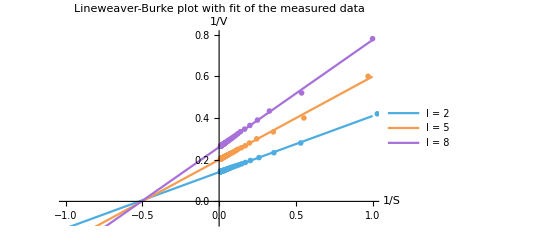

| V_maxI = 2 | V_maxI = 5 | V_maxI = 8
Estimated V_max | 7.2 | 5.1 | 4.
Calculated V_max | 7.12978 | 5.00229 | 3.84343
Estimated K_M | 2. | 2. | 2.
Calculated K_m | 1.91996 | 1.99348 | 1.97541

```mathematica
fit2 =  LinearModelFit[1/dataI2⟦2 ;;⟧, x, x];
fit5 = LinearModelFit[1/dataI5⟦2 ;;⟧, x, x];
fit8 = LinearModelFit[1/dataI8⟦2 ;;⟧, x, x];

fitPlot = Plot[{fit2[x], fit5[x], fit8[x]}, {x,-1,1}, PlotTheme->"PastelColor",PlotRange->All, PlotLegends-> {"I = 2", "I = 5", "I = 8"}];
consDataPlot = ListPlot[{1/dataI2⟦2 ;;⟧, 1/dataI5⟦2 ;;⟧, 1/dataI8⟦2 ;;⟧},PlotTheme->{"BoldScheme", "PastelColor"}, PlotRange->All];

Show[fitPlot, consDataPlot,PlotLabel-> "Lineweaver-Burke plot with fit of the measured data",
AxesLabel-> {"1/S", "1/V"}, PlotRange-> {{-1, 1}, {-0.1,0.8}}]

Vmax2 = 1/fit2[0];
Vmax5= 1/fit5[0];
Vmax8 = 1/fit8[0];
Km2 = -((x/.Solve[fit2[x] == 0, Reals])^-1)⟦1⟧ ;
Km5 = -((x/.Solve[fit5[x] == 0, Reals])^-1)⟦1⟧ ;
Km8 = -((x/.Solve[fit8[x] == 0, Reals])^-1)⟦1⟧ ;


Grid[{{"","V_maxI = 2", "V_maxI = 5","V_maxI = 8"},{"Estimated V_max",7.2, 5.1, 4.0},{"Calculated V_max", Vmax2, Vmax5, Vmax8},{"Estimated K_M",2.0, 2.0, 2.0}, {"Calculated K_m" , Km2, Km5, Km8}},Frame->All]

Km =
```

Conclusions
It is difficult to accurately determine the V_max and K_m by examining the Michaelis-Menten plots. The values determined by making a Lineweaver-Burk plot are probably more accurate than the ones estimated by eye, but should also be compared to other ways to determine the values, for example Hans-Woolf or Eadie-Hofstee, because Lineweaver-Burk estimates are sometimes marked as  estimates with a big error. Both methods of plotting may indicate datapoints that are “outliers” and whether there is substrate inhibition.

Because the Vmax increases, but the Km stays the same, we can conclude that the inhibitor we investigated here is  a noncompetitive inhibitor.

3. Ionic channels

#### Introduction: About ion channels

-Graphics-Figure 1: An Ion channel in closed and open state.
From: http://blog.canacad.ac.jp/wpmu/15matser/2011/09/14/4-1-passive-transport/

Cellular membranes contain ionic channels (see figure 1). These channels can be regarded as special enzymes for mediation ion transportation through the membrane. The channels considered here can exist in three states: S_1, S_2 and S_3. S_1 and S_3 represent closed states on either side of the membrane. When the channel is closed, no ions can pass trough the channel. S_2 is an open state. On a given cell, there are a number of channels and the fractions of channels in states S_1, S_2 and S_3 are designated x, y and z, respectively. These fractions lie between 0 and 1.

Transitions between the states go via the following schematic diagram:
S_1(⇌_k_3)^k_1 S_2→^k_2 S_3
Here, k_1,k_2 and k_3 are positive rate constants. The system of differential equations for this system is:

dx/dt=- k_1 x+k_3 y

dy/dt=k_1 x-(k_2+k_3) y

dz/dt=k_2 y

Methods 
To study the transitions between the different states of ion channels, firstly, we sketch the transitioning of channels between states in the x,y plane, assuming that k_1=2, k_2=2 and k_3=1. Secondly, we solve the equations x, y and z as a function of time, starting from two different initial conditions: (1) x = 1, y = 0, z = 0; (2)  x = 0, y = 1, z = 0. Then, we solve the equations again, but with different rate constants: k_1=0, k_2=2 and k_3=1. We start from the second set of initial conditions we just defined. Furthermore, we then calculate x and z in terms of k_2 and k_3, assuming k_1=0 and k_2,k_3 are arbitrary positive numbers.

Results and Discussion

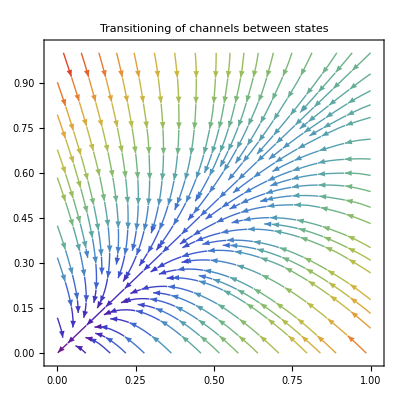

```mathematica
ClearAll["Global`*"]

dx[x_,y_]=-2 x+y;
dy[x_,y_]=2 x-(2+1) y;
dz[x_]=2 y;

StreamPlot[{dx[x,y],dy[x,y]},{x,0,1},{y,0,1}, PlotLabel->"Transitioning of channels between states", StreamColorFunction->"Rainbow"]
```

In the above plot the first thing we notice is that no matter from what fraction in x and/or y the system starts, we always end up with 0 enzymes in the S_1 or S_2 state. This makes sense, because the transition to S_3 is irreversible (there is no “back-reaction”). The second thing is the difference between starting from a high fraction in S_1 (a high x) or starting from a high fraction in S_2 (a high y). When we start with a high x, the maximum of y is higher then the other way around (the maximum of x when you start with a high y. This is because when we start with a high fraction of y (many enzymes in state S_2) the enzymes will go into state S_3 faster (and stay there) then when we start with a high x.

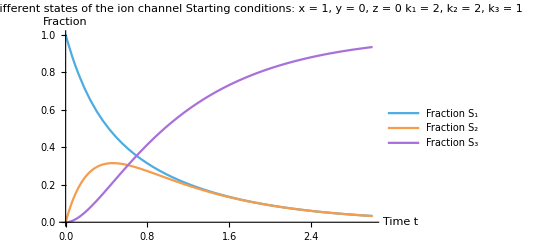

```mathematica
Remove[x, y, z]

solvedFirst[t_]=NDSolve[{x'[t]==-2 x[t]+y[t],y'[t]==2 x[t]-(2+1) y[t],z'[t]==2 y[t],x[0]==1,y[0]==0,z[0]==0},{x[t],y[t],z[t]},{t,0,3}];

Plot[Evaluate[{x[t]/.solvedFirst[t],y[t]/.solvedFirst[t],z[t]/.solvedFirst[t]}],{t,0,3},
AxesLabel->{"Time t", "Fraction"},
PlotLegends->{"Fraction S_1","Fraction S_2","Fraction S_3"},
PlotTheme->"Pastel",
PlotLabel-> "Population of different states of the ion channel\n Starting conditions: x = 1, y = 0, z = 0\n k_1 = 2, k_2 = 2, k_3 = 1"]
```

We see here the same behavior as described in the x,y plane plot. We start with all the enzymes in state S_1, they will go through state S_2and end up in state S_3. There will be transitions from S_2 back to S_1, and that is why it takes the system longer to go all enzymes in state S_3 than it would if the reaction of S_1 to S_2 would also be irreversible.

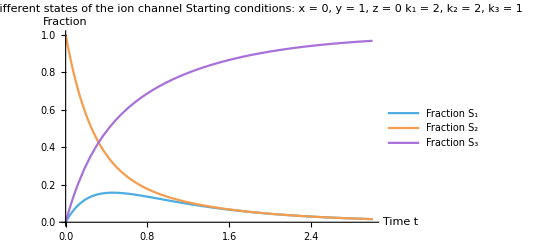

```mathematica
solvedSecond[t_]=NDSolve[{x'[t]==-2 x[t]+y[t],y'[t]==2 x[t]-(2+1) y[t],z'[t]==2 y[t],x[0]==0,y[0]==1,z[0]==0},{x[t],y[t],z[t]},{t,0,3}];

Plot[Evaluate[{x[t]/.solvedSecond[t],y[t]/.solvedSecond[t],z[t]/.solvedSecond[t]}],{t,0,3},
AxesLabel->{"Time t", "Fraction"},
PlotLegends->{"Fraction S_1","Fraction S_2","Fraction S_3"},
PlotTheme->"Pastel",
PlotLabel-> "Population of different states of the ion channel\n Starting conditions: x = 0, y = 1, z = 0\n k_1 = 2, k_2 = 2, k_3 = 1"]
```

Again, the same behavior as described in the x,y plane plot. All the enzymes start in state S_2, they will end up in state S_3. In this graph we see the transition from S_2 back to S_1 happening: there is a slight peak in the fraction in S_1. We also see the difference: the fraction S_3 goes up faster then in the previous plot where the enzymes all started in state S_1. This is because not all enzymes have to transition through another state (S_2 in the graph above this one) first.

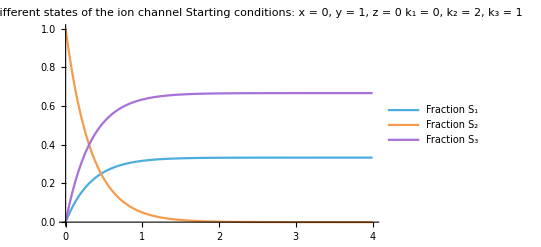

```mathematica
Remove[x,y,z]

solvedC1[t_]=NDSolve[{x'[t]==y[t],y'[t]==-(2+1) y[t],z'[t]==2 y[t],x[0]==0,y[0]==1,z[0]==0},{x[t],y[t],z[t]},{t,0,4}];

Plot[Evaluate[{x[t]/.solvedC1[t],y[t]/.solvedC1[t],z[t]/.solvedC1[t]}],{t,0,4},PlotLegends->{"Fraction S_1","Fraction S_2","Fraction S_3"}, PlotTheme->"Pastel", PlotLabel-> "Population of different states of the ion channel\n Starting conditions: x = 0, y = 1, z = 0\n k_1 = 0, k_2 = 2, k_3 = 1"]
```

When we model the system with k_1 being 0, the enzyme also can’t leave the S_1 state anymore. If we start with all the enzymes in state S_2, the enzyme will end up in state S_1 and S_3, the fraction between these two depending on the rates k_2 and k_3. Since k_2 = 2 and k_3 = 1, one third of the enzymes will end up in state will end up in state S_1 and two thirds will end up in state S_3; this is exactly what we see happening in the above figure.

```mathematica
Remove[x,y,z, k1, k2, k3]

DSolve[{x'[t]==k3*y[t],y'[t]==-(k2+k3)* y[t],z'[t]==k2 * y[t], x[0] == 0, y[0] == 1, z[0] == 0},{x[t],y[t],z[t]},t]
```

{{x[t]→-((-1+ⅇ^((-k2-k3) t)) k3)/(k2+k3),y[t]→ⅇ^((-k2-k3) t),z[t]→-((-1+ⅇ^((-k2-k3) t)) k2)/(k2+k3)}}

Conclusions
We can conclude that how fast the system ends up in a steady state depends heavily on the rate constants. We can also conclude, that if the reaction between S_2 and S_3 would be reversible, not all enzymes would end up in state S_3.